## Integrali, funkcije več spremenljivk in funkcijske vrste

## Integrali

Integrale računamo s pomočjo ukaza Integrate[ ], oz. NIntegrate[ ].

```mathematica
?Integrate
```

1. Izračunajte naslednje integrale.
	a) ∫ x^4/(1+x^2) ⅆx
	b) ∫_0^∞ x^2 ⅇ^(-2x) ⅆx
	c) ∫_0^1 ⅇ^(x^2)  ⅆx

```mathematica
Integrate[x^4/(1+x^2),x]
Integrate[x^2 E^(-2 x),{x,0,Infinity}]
NIntegrate[E^(x^2),{x,0,1}]
```

-x+x^3/3+ArcTan[x]

1/4

1.46265

2. Izračunajte naslednje integrale.
	a) ∫ 1/(√(2-5x)) ⅆx = -2/5√(2-5x) + C
	b) ∫_1^2 (x^2+1/x^4) ⅆx = 21/8
	c) ∫_0^(π/4) sin(4x) ⅆx = 1/2
	d) ∫_0^(π/4) (sin(2x))/(cos^4(x)) ⅆx = 1
	e) ∫_0^π x sin(x)  ⅆx = π
	f) ∫_-2^2 x^2 sin(x)  ⅆx = 0

```mathematica
Integrate[1/(Sqrt[2-5x]),x]
Integrate[x^2+x^-4, {x,1,2}]
Integrate[Sin[4x], {x,0, Pi/4}]
Integrate[Sin[2x]/Cos[x]^4, {x, 0, Pi/4}]
Integrate[x*Sin[x], {x, 0, Pi}]
```

-2/5 √(2-5 x)

21/8

1/2

1

π

Uporaba integralov: (y = f(x))
a) Ploščina lika: S = ∫_a^b  f(x)dx, S = ∫_a^b  (f(x)-g(x))dx
b) Ločna dolžina: s = ∫_a^b  √(1+(y')^2)dx
c) Prostornina rotacijskega telesa: V = π ∫_a^b  y^2 dx
d) Površina rotacijskega telesa: P = 2π ∫_a^b  y √(1+(y')^2)dx

3. Izračunajte ploščino lika med parabolo y = x^2+2 in tangentama v točkah A(-1,3) in B(2,6).
   Parabolo in tangenti tudi skicirajte.
   Rezultat: p = 9/4

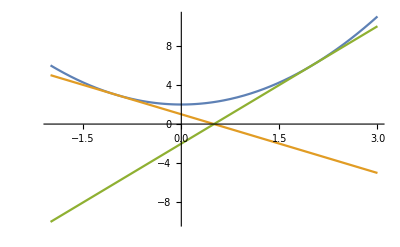

1/2

9/4

```mathematica
y=x^2+2; 
(* Točke za izračun odvoov *)
a=-1;ya=3; b=2; yb=6;

(* odvod v točki *)
kt1=D[y,x]/.x->a;
(* enačba premice y=kx+n *)
y1=kt1*x+(ya-kt1*a);

kt2=D[y,x]/.x->b;
y2=kt2*x+(yb-kt2*b);

Plot[{y,y1,y2},{x,-2,3}]
(* Presečišče tangent *)
c=x/.Flatten[Solve[y1==y2,x]]
(*Solve[y1==y2,x]
Flatten[Solve[y1==y2,x]] *)

(* Ploščina območja - meje integralov so že podane s točkami v navodilih in presečišča *)
S=Integrate[y-y1,{x,a,c}]+Integrate[y-y2,{x,c,b}]
```

4. Izračunajte ploščino lika, ki je omejen s krivuljo y = 6/(5 - 4x - x^2) in premicami x = 2, x = 3 ter abscisno osjo.
Rezultat: p = ln(7/4)

6/(5-4 x-x^2)

2

3

Log[7/4]

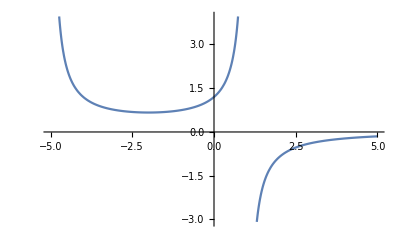

```mathematica
(* Clear[Global`] *)
y=6/(5-4x-x^2)
x1 = 2
x2 = 3
FullSimplify[-Integrate[y ,{x,x1, x2}]]
Plot[y, {x,-5,5}]
```

5. Izračunajte prostornino in površino rotacijskega telesa, ki nastane, če krivuljo y = √(1 - x^2), 0 < x < 1, zavrtimo okoli osi x.
Rezultati: V = 2π/3, P = 2π

(2 π)/3

2 π

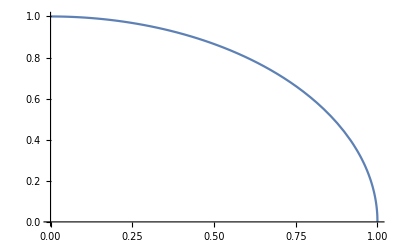

```mathematica
Clear["Global`*"]
y=Sqrt[1-x^2];
(* Prostornina *)
V=Pi*Integrate[y^2, {x,0,1}]
(* Površina *)
P=2Pi Integrate[y Sqrt[1+D[y,x]^2], {x,0,1}]
(* Slika *)
Plot[y,{x,0,1}] (* četrtina kroga, zavrtiš čez x os in dobiš polovico krogle *)
(* V_krogle = 4Pi r^3/3, P_krogle = 4 Pi r^2 *)
```

6. Izračunajte dolžino loka krivulje y = ln(1 - x^2), 0 < x < 1/2.
	Rezultat: s = ln3 - 1/2.

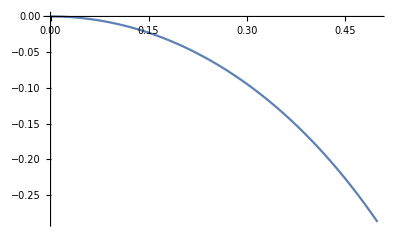

-1/2+Log[3]

```mathematica
Clear["Global`*"]
y=Log[1-x^2];
Plot[y, {x, 0,1/2}]
(* Dolžina loka *)
FullSimplify[Integrate[Sqrt[1+D[y,x]^2], {x, 0, 1/2}]]
```

## Funkcije več spremenljivk

Območja v ravnini rišemo s pomočjo ukaza RegionPlot[ ].
Krivulje v ravnini rišemo s pomočjo ukaza ContourPlot[ ].
Grafe v treh dimenzijah rišemo s pomočjo ukaza Plot3D[ ].

```mathematica
?RegionPlot
?ContourPlot
?Plot3D
```

7. a) Narišite definicijsko območje funkcije f(x,y) = ln(x^2 + y).
   b) Narišite nivojske krivulje funkcije f(x,y) = x^2 + y^2, za c = 1,4,9,16.
   c) Narišite graf funkcije f(x,y) = x^2 + y^2.

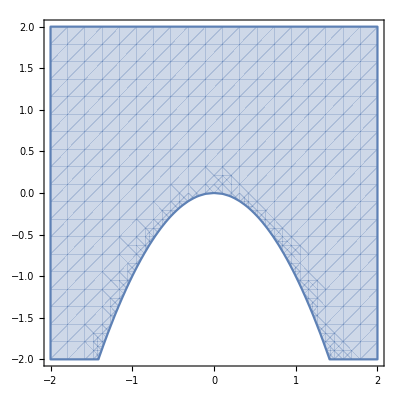

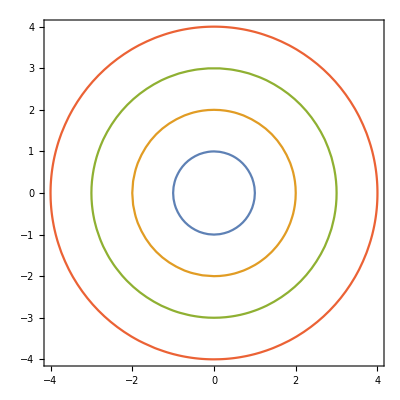

-Graphics3D-

```mathematica
(* Rešitev primera a): *)
RegionPlot[x^2+y>0,{x,-2,2},{y,-2,2}]
(* Rešitev primera b): *)
ContourPlot[{x^2+y^2==1,x^2+y^2==4,x^2+y^2==9,x^2+y^2==16},{x,-4,4},{y,-4,4}]
(* Rešitev primera c): *)
Plot3D[x^2+y^2,{x,-4,4},{y,-4,4}]

Plot3D[x^2+y^2,{x,-4,4},{y,-4,4}], RegionFunction-> Function[{x,y,z}, x^2+y^2≤ 16]
```

8. Izračunajte vse prve in druge parcialne odvode funkcije f(x,y) = arctan((x + y)/(1 - x y)).

```mathematica
Clear["Global`*"]
Clear[x,y,f]
(* Definicija funkcije: *)
f[x_,y_]=ArcTan[(x+y)/(1-x y)];
(* Prva parcialna odvoda: *)
fx=Simplify[D[f[x,y],x]]
fy=Simplify[D[f[x,y],y]]
(* Drugi parcialni odvodi: *)
fxx=Simplify[D[f[x,y],x,x]]
fxy= Simplify[D[f[x,y],x,y]]
fyx= Simplify[D[f[x,y],y,x]]
fyy= Simplify[D[f[x,y],y,y]]

Clear[x,y,f]
f=ArcTan[(x+y)/(1-x y)];
fxx =Simplify[D[f,x,x]]
fxy=Simplify[D[f,x,y]]
fyx=Simplify[D[f,y,x]]
fyy=Simplify[D[f,y,y]]
```

1/(1+x^2)

1/(1+y^2)

-(2 x)/((1+x^2)^2)

0

0

-(2 y)/((1+y^2)^2)

-(2 x)/((1+x^2)^2)

0

0

-(2 y)/((1+y^2)^2)

Stacionarno ali kritično točko (x0,y0) funkcije z = f(x,y) dobimo tam, kjer je ∂z/∂x = 0 in ∂z/∂y = 0. Izračunamo še druge parcialne odvode v stacionarni točki (x0,y0): A = ∂^2z/∂x^2(x0,y0), B = ∂^2z/∂x∂y(x0,y0) in C = ∂^2z/∂y^2(x0,y0). V stacionarni točki dobimo lokalni ekstrem, če je Δ = AC - B^2 > 0. Če je poleg tega A > 0 imamo lokalni minimum, če pa je A < 0 imamo lokalni maksimum. Če je Δ < 0 nimamo ekstrema ampak sedlo. Če je Δ = 0 lahko ekstrem je, ali pa ga ni, odvisno od višjih odvodov.

9. Izračunajte tretji parcialni odvod ∂^3 f/∂y^2 ∂z (f_{yyz}) za funkcijo f (x,y,z) = x^2/(y^2 + z^2).
    Rezultat : ∂^3 f/∂y^2 ∂z = -8 x^2 (5 y^2 z - z^3)/(y^2 + z^2)^4

```mathematica
Clear["Global`*"]
f=x^2/(y^2+z^2);
fyyz=Simplify[D[f, y,y,z]]
fyzy=Simplify[D[f, y,z,y]]
fzyy=Simplify[D[f, z,y,y]]
```

(8 x^2 z (-5 y^2+z^2))/((y^2+z^2)^4)

(8 x^2 z (-5 y^2+z^2))/((y^2+z^2)^4)

(8 x^2 z (-5 y^2+z^2))/((y^2+z^2)^4)

10. Poiščite stacionarne točke in klasificirajte lokalne ekstreme funkcije f(x,y) = ⅇ^(2x)(x + y^2 + 2 y).

```mathematica
Clear["Global`*"]
Clear[x,y,f]
(* Definicija funkcije: *)
f[x_,y_]=E^(2x) (x+y^2+2y);
(* Določitev stacionarnih točk: *)
fx=D[f[x,y],x];
fy=D[f[x,y],y];
sol=Solve[{fx==0,fy==0},{x,y}];
st=Flatten[{x,y}/.sol]
(* Klasifikacija lokalnih ekstremov: *)
fxx=D[f[x,y],x,x]; a=fxx/.{x->st[[1]],y->st[[2]]};
fxy=D[f[x,y],x,y]; b=fxy/.{x->st[[1]],y->st[[2]]};
fyy=D[f[x,y],y,y]; c=fyy/.{x->st[[1]],y->st[[2]]};
Delta=a c - b^2;
Which[Delta>0,Which[a>0,Print[Lokalni minimum],a<0,Print[Lokalni maksimum]],Delta<0,Print[Sedlo],Delta=0,Print[Ne vemo]]
Plot3D[E^(2x) (x+y^2+2y),{x,-1,1},{y,-2,0}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{1/2,-1}

Lokalni minimum

-Graphics3D-

11. Poiščite stacionarne točke in klasificirajte lokalne ekstreme funkcije f(x,y) = x^3 + y^3 - 3xy.
    Rezultati: T(0,0) sedlo, T(1,1) lokalni minimum.

```mathematica
Clear["Global`*"]
Clear[x,y,f]
(* Definicija funkcije: *)
f[x_,y_]=x^3+y^3-3x y;
(* Določitev stacionarnih točk: *)
fx=D[f[x,y],x];
fy=D[f[x,y],y];
sol=Solve[{fx==0,fy==0},{x,y}];
st=Flatten[{x,y}/.sol]
(* Klasifikacija lokalnih ekstremov: *)
fxx=D[f[x,y],x,x]; a=fxx/.{x->st[[1]],y->st[[2]]};
fxy=D[f[x,y],x,y]; b=fxy/.{x->st[[1]],y->st[[2]]};
fyy=D[f[x,y],y,y]; c=fyy/.{x->st[[1]],y->st[[2]]};
Delta=a c - b^2;

fxx2=D[f[x,y],x,x]; a2=fxx2/.{x->st[[3]],y->st[[4]]};
fxy2=D[f[x,y],x,y]; b2=fxy2/.{x->st[[3]],y->st[[4]]};
fyy2=D[f[x,y],y,y]; c2=fyy2/.{x->st[[3]],y->st[[4]]};
Delta2=a2 c2 - b2^2;


Which[Delta>0,Which[a>0,Print[Lokalni minimum],a<0,Print[Lokalni maksimum]],Delta<0,Print[Sedlo],Delta=0,Print[Ne vemo]]

Which[Delta2>0,Which[a2>0,Print[Lokalni minimum],a2<0,Print[Lokalni maksimum]],Delta2<0,Print[Sedlo],Delta2=0,Print[Ne vemo]]

s1 = Plot3D[x^3+y^3-3x y,{x,-2,2},{y,-2,2}];
s2 = Graphics3D[{Red, Sphere[{0,0,f[x,y]/.{x->0, y->0}}, 0.05], Red, Sphere[{1,1,f[x,y]/.{x->1, y->1}}, 0.05]}];
Show[s1,s2]
```

{0,0,1,1,-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),-(-1)^(1/3)}

Sedlo

Lokalni minimum

-Graphics3D-

12. Izračunajte dvojni integral ∫_0^1 ( ∫_(1-y)^(1+y) (x^2-2 x y+y^2) ⅆx) ⅆy.

1/3

-Graphics3D-

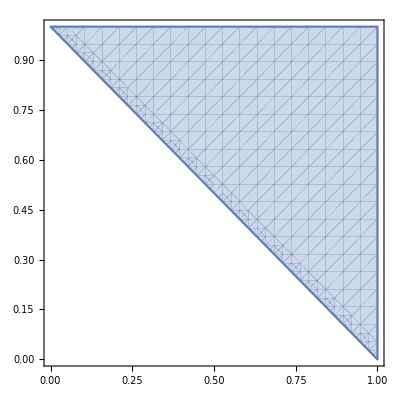

```mathematica
Integrate[x^2-2x y+y^2,{y,0,1},{x,1-y,1+y}]
Plot3D[x^2-2x y+y^2, {y,0,1}, {x, 1-y, 1+y}]
RegionPlot[{y≥ 0 && y≤1 && x≥ 1-y && x≤  1+y}, {x,0,1}, {y,0,1}]
```

## Funkcijske vrste

Vsoto vrste izračunamo s pomočjo ukaza Sum[ ].

```mathematica
?Sum
```

13. Določite območje konvergence potenčne vrste   ∑ _(n=0)^∞ n^2/2^n(x-1)^n.
Rezultat: (-1,3)

```mathematica
Clear[a,n];
(* splošni člen *)
a[n_]:=n^2/2^n
(* Konvergenčni polmer: *)
R=Limit[Abs[a[n]/a[n+1]],n->Infinity]
(* Krajišča intervala: *)
Sum[(n^2/2^n (x-1)^n)/.x->-1,{n,0,Infinity}]
Sum[(n^2/2^n (x-1)^n)/.x->3,{n,0,Infinity}]
(* interval od -1 do 3 brez krajišč je območje konvergence *)
```

2

Sum::div: Sum does not converge.

∑_(n=0)^∞ (-1)^n n^2

Sum::div: Sum does not converge.

∑_(n=0)^∞ n^2

14. Določite območje konvergence potenčne vrste   ∑ _(n=0)^∞ 1/(√(3n+2))(3x+1)^n.
	Rezultat: [-2/3,0)

```mathematica
Clear[a,n];
(* splošni člen *)
(* a=-1/3, an=3^n/sqrt(3^n+2) *)
a[n_]:=3^n/Sqrt[3n+2]
(* Konvergenčni polmer: *)
R=Limit[Abs[a[n]/a[n+1]],n->Infinity]
(* Zagotovo konvergira *)
aa=-1/3;
{aa-R, aa+R}

(* Krajišča intervala: *)
Sum[a[n](x-aa)^n/.x->-2/3,{n,0,Infinity}] //N
Sum[a[n](x-aa)^n/.x->0,{n,0,Infinity}]
```

1/3

{-2/3,0}

0.452628

Sum::div: Sum does not converge.

∑_(n=0)^∞ 1/(√(2+3 n))

Funkcijo razvijemo v Taylorjevo vrsto s pomočjo ukazov Series[ ] in Normal[ ].

```mathematica
?Series
?Normal
```

```mathematica
Series[Sin[x],{x,0,10}] (* Na koncu je ostanek *)
Normal[Series[Sin[x],{x,0,10}]] (* Na koncu ni ostanka *)
Normal[Series[Cos[x],{x,0,10}]]
Normal[Series[E^x,{x,0,10}]]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

x-x^3/6+x^5/120-x^7/5040+x^9/362880

1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800

15. Razvijte funkcijo f(x) = x^2/(√((1+x^2)^3))v Taylorjevo vrsto okoli točke a = 0 do potence n = 12.

```mathematica
Clear["Global`*"]
f=x^2/Sqrt[(1+x^2)^3];
Normal[Series[f, {x,0,12}]]
```

x^2-(3 x^4)/2+(15 x^6)/8-(35 x^8)/16+(315 x^10)/128-(693 x^12)/256

16. Z uporabo ustrezne Taylorjeve vrste izračunajte približno vrednost 29^(1/3)na 5 decimalnih mest natančno.
	Rezultat: 3.07232

```mathematica
Normal[Series[3(1+x)^(1/3),{x,0,12}]]

Table[Normal[Series[3(1+x)^(1/3),{x,0,n}]]/.x->2/27,{n,0,9}]//N

(* Prikaz pri katerem členu se 5 decimalka ne spreminja več *)
N[Table[Normal[Series[3(1+x)^(1/3),{x,0,n}]]/.x->2/27,{n,0,9}], 11]
```

3+x-x^2/3+(5 x^3)/27-(10 x^4)/81+(22 x^5)/243-(154 x^6)/2187+(374 x^7)/6561-(935 x^8)/19683+(21505 x^9)/531441-(55913 x^10)/1594323+(147407 x^11)/4782969-(1179256 x^12)/43046721

{3.,3.07407,3.07225,3.07232,3.07232,3.07232,3.07232,3.07232,3.07232,3.07232}

{3.,3.0740740741,3.0722450846,3.0723203516,3.0723166348,3.0723168367,3.072316825,3.0723168257,3.0723168257,3.0723168257}

17. S pomočjo razvoja v Taylorjevo vrsto do vključno pete potence izračunajte približno vrednost integrala ∫_0^2 (sin(x))/x ⅆx.
	Rezultat: 1.6089.

```mathematica
(* numerična rešitev *)
NIntegrate[Sin[x]/x, {x,0,2}]
(* s taylorjevo vrsto *)
Normal[Series[Sin[x]/x,{x,0,5}]]

Integrate[Normal[Series[Sin[x]/x,{x,0,5}]],{x,0,2}]//N

Table[Integrate[Normal[Series[Sin[x]/x,{x,0,n}]],{x,0,2}],{n,0,11}] //N
```

1.60541

1-x^2/6+x^4/120

1.60889

{2.,2.,1.55556,1.55556,1.60889,1.60889,1.60526,1.60526,1.60542,1.60542,1.60541,1.60541}